```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

## Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

< -MemDB- {A,bNum,bsquare,data,EN,etav,MN,Pb32by2Pi,PL,zta}>

```mathematica
MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B}],{PL,zta}]//Union
```

{{-4,⟨0.786(34)⟩_(RowBox[{)},{-3,⟨0.540(12)⟩_(RowBox[{)},{-2,⟨0.2944(36)⟩_(RowBox[{)},{-1,⟨0.09077(75)⟩_(RowBox[{)}}

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults, numParams},numFs=Length[fitParams[[1]]];
numParams=Length[fitParams];
modelvaluej[j_]:=Module[{datafitParams},datafitParams=Table[fitParams[[k,j]],{k,numParams}];
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
jackknifeResults];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
WeightList = {};
Do[
ε=10^-6;
σ=(MakeErrBars[{{1,xyJKf[[ii]][[3]]}}][[1]][[2]][[1]][[2]]);
AppendTo[WeightList,1/Max[σ,ε]^2], {ii, Length[xyJKf]}];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

JackknifeFit4DGaussianCons[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,{model, c>d},If[init===Automatic,para,init],vari,Weights->WeightList];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
(a^x1)*Exp[-c*Pb^2]*Exp[-(d^x1)*f*(x3^g)]
```

a^x1 ⅇ^(-c Pb^2-d^x1 f x3^g)

```mathematica
FourierTransform[(a^x1)*Exp[-c*Pb^2]*Exp[-(d^x1)*f*(x3^g)],Pb,x]
```

(a^x1 ⅇ^(-x^2/(4 c)-d^x1 f x3^g))/(√2 √c)

## Main Code:

```mathematica
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]],fitParams[[4]][[j]],fitParams[[5]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelJackk[model_, fitParam_, multipliar_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParam];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=fitParam[[j]];
model[datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults*multipliar
];
```

```mathematica
FourierA2bReeta[b2_,P1_, etafit_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B,fourierA2Bforx,fourierREA2Bforx},
dataforfitA2B = Select[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1, bNum->even}],{etav, Pb32by2Pi, bsquare,data}],#[[1]]>=6&&#[[1]]<=9&&#[[3]]>=8&];
(*dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];*)
Print[" 8 are SELECTED for fit!"];
Print[" are SELECTED for fit!"];

modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_,g_}]:=(a^x1)*Exp[-c*x2^2]*Exp[-(d^x1)*f*(x3^g)];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, Pb32by2Pi, bsquare,{a,c, d,f,g}],{{a, 0.73703086},{c,0.000282}, {d,1.1452}, {f,0.148}, {g,0.629}},{n,Pb32by2Pi, bsquare}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n  = ",b2, "  = ",P1];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA2B =fitParasA2B[[1]];
fitcA2B=fitParasA2B[[2]];
fitdA2B =fitParasA2B[[3]];
fitfA2B =fitParasA2B[[4]];
fitgA2B =fitParasA2B[[5]];

fourierA2B[x_, {fitaA2B_, fitcA2B_, fitdA2B_, fitfA2B_, fitgA2B_}] :=((fitaA2B^etafit) Exp[-(x^2/(4 fitcA2B))-fitdA2B^etafit fitfA2B b2^fitgA2B])/(Sqrt[2] Sqrt[fitcA2B]);
Print["",etafit," is SELECTED for plot!"];
fourieA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{fitaA2B, fitcA2B, fitdA2B , fitfA2B, fitgA2B}, x];
fourierA2Bforx=fourierREA2Bforx;
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
];
```

```mathematica
FourierA2bReeta[9,-2,10]
```

8 are SELECTED for fit!

are SELECTED for fit!

Fitting:    -> () =                                                           -6
{⟨0.878(41)⟩_(2902J), ⟨-990(910) × 10  ⟩_(2902J), ⟨1.1297(45)⟩_(2902J), ⟨0.403(88)⟩_(2902J), ⟨0.454(49)⟩_(2902J)}, chisquareDoF = 1.20022
  = 9  = -2

10 is SELECTED for plot!

-Graphics-

8 are SELECTED for fit!

are SELECTED for fit!

Fitting:    -> () = {⟨0.8647(22)⟩_(2902J), ⟨0.00189(11)⟩_(2902J), ⟨1.0480(29)⟩_(2902J), ⟨0.2754(49)⟩_(2902J), ⟨0.5094(42)⟩_(2902J)}, chisquareDoF = 6.55747
  = 9  = -2

10 is SELECTED for plot!

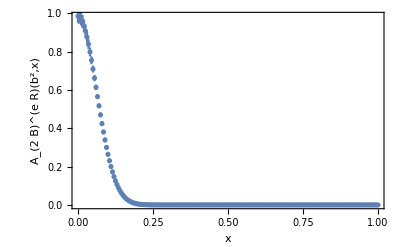

```mathematica
FourierA2bReeta[9,-2,10]
```

8 are SELECTED for fit!

are SELECTED for fit!

Fitting:    -> () = {⟨0.8659(51)⟩_(2902J), ⟨0.00195(13)⟩_(2902J), ⟨1.0722(72)⟩_(2902J), ⟨0.2744(98)⟩_(2902J), ⟨0.5111(85)⟩_(2902J)}, chisquareDoF = 2.13574
  = 9  = -3

10 is SELECTED for plot!

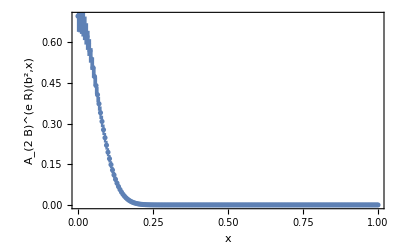

```mathematica
FourierA2bReeta[9,-3,10]
```

8 are SELECTED for fit!

are SELECTED for fit!

Fitting:    -> () = {⟨0.875(13)⟩_(2902J), ⟨0.00204(23)⟩_(2902J), ⟨1.112(19)⟩_(2902J), ⟨0.251(21)⟩_(2902J), ⟨0.524(20)⟩_(2902J)}, chisquareDoF = 0.556553
  = 9  = -4

10 is SELECTED for plot!

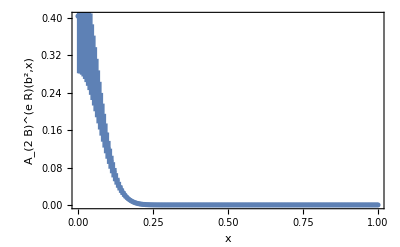

```mathematica
FourierA2bReeta[9,-4,10]
```

8 are SELECTED for fit!

are SELECTED for fit!

Fitting:    -> () =                                                           -6
{⟨0.7982(70)⟩_(2902J), ⟨220(270) × 10  ⟩_(2902J), ⟨1.1625(40)⟩_(2902J), ⟨0.2084(95)⟩_(2902J), ⟨0.554(13)⟩_(2902J)}, chisquareDoF = 3.36293
  = 9  = -2

10 is SELECTED for plot!

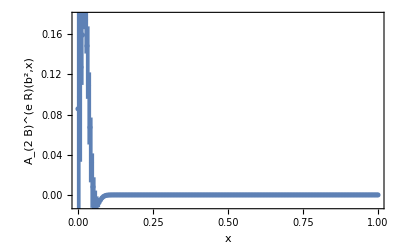

```mathematica
FourierA2bReeta[9,-2,10]
```

8 are SELECTED for fit!

are SELECTED for fit!

Fitting:    -> () =                                                          -6
{⟨0.777(16)⟩_(2902J), ⟨740(330) × 10  ⟩_(2902J), ⟨1.1673(87)⟩_(2902J), ⟨0.192(23)⟩_(2902J), ⟨0.599(33)⟩_(2902J)}, chisquareDoF = 1.70388
  = 9  = -3

10 is SELECTED for plot!

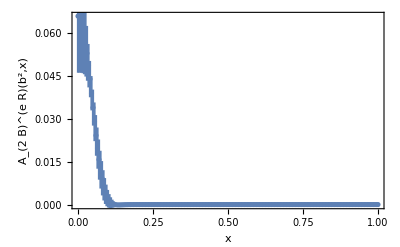

```mathematica
FourierA2bReeta[9,-3,10]
```

8 are SELECTED for fit!

are SELECTED for fit!

Fitting:    -> () = {⟨0.707(28)⟩_(2902J), ⟨0.00123(55)⟩_(2902J), ⟨1.140(27)⟩_(2902J), ⟨0.104(34)⟩_(2902J), ⟨0.78(11)⟩_(2902J)}, chisquareDoF = 0.576429
  = 9  = -4

10 is SELECTED for plot!

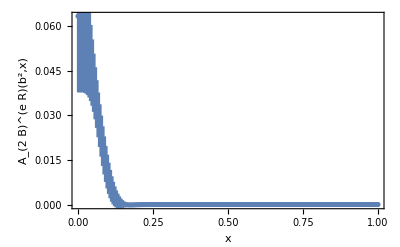

```mathematica
FourierA2bReeta[9,-4,10]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨1.32(16)⟩_(2902J), ⟨0.01142(67)⟩_(2902J), ⟨0.0746(43)⟩_(2902J), ⟨0.477(17)⟩_(2902J)}, chisquareDoF = 1.54749
  = 9  = -2

12 is SELECTED for plot!

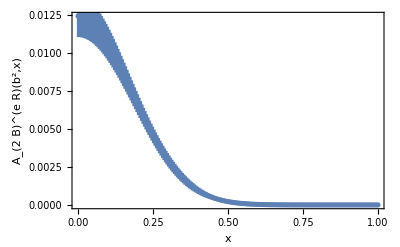

```mathematica
FourierA2bReeta[9,-2,6,3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨1.15(38)⟩_(2902J), ⟨0.0151(16)⟩_(2902J), ⟨0.088(12)⟩_(2902J), ⟨0.473(43)⟩_(2902J)}, chisquareDoF = 0.841819
  = 9  = -3

12 is SELECTED for plot!

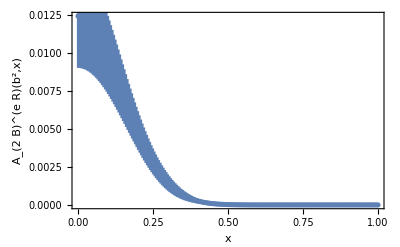

```mathematica
FourierA2bReeta[9,-3,6,3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨0.89(70)⟩_(2902J), ⟨0.0162(29)⟩_(2902J), ⟨0.069(19)⟩_(2902J), ⟨0.496(93)⟩_(2902J)}, chisquareDoF = 0.504828
  = 9  = -4

12 is SELECTED for plot!

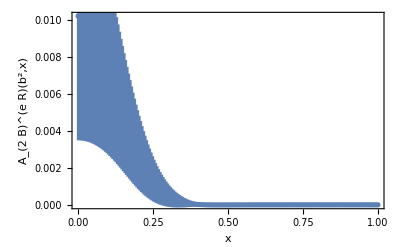

```mathematica
FourierA2bReeta[9,-4,6,3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨1.179(66)⟩_(2902J), ⟨0.00865(29)⟩_(2902J), ⟨0.0577(16)⟩_(2902J), ⟨0.4560(83)⟩_(2902J)}, chisquareDoF = 4.77692
  = 9  = -1

8 is SELECTED for plot!

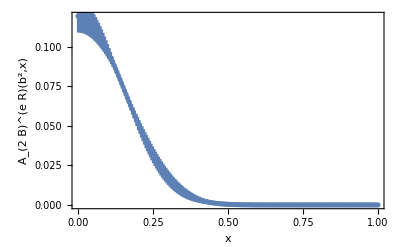

```mathematica
FourierA2bReeta[9,-1,6,3,8]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨1.32(16)⟩_(2902J), ⟨0.01142(67)⟩_(2902J), ⟨0.0746(43)⟩_(2902J), ⟨0.477(17)⟩_(2902J)}, chisquareDoF = 1.54749
  = 9  = -2

8 is SELECTED for plot!

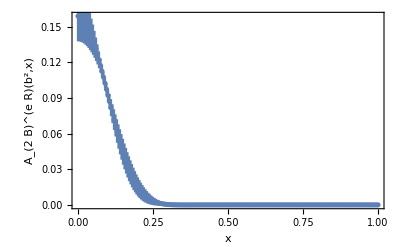

```mathematica
FourierA2bReeta[9,-2,6,3,8]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨1.15(38)⟩_(2902J), ⟨0.0151(16)⟩_(2902J), ⟨0.088(12)⟩_(2902J), ⟨0.473(43)⟩_(2902J)}, chisquareDoF = 0.841819
  = 9  = -3

8 is SELECTED for plot!

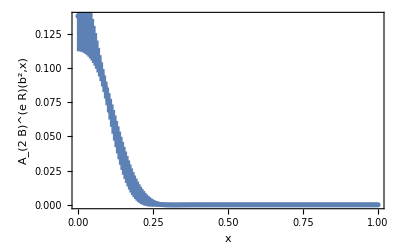

```mathematica
FourierA2bReeta[9,-3,6,3,8]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨0.89(70)⟩_(2902J), ⟨0.0162(29)⟩_(2902J), ⟨0.069(19)⟩_(2902J), ⟨0.496(93)⟩_(2902J)}, chisquareDoF = 0.504828
  = 9  = -4

8 is SELECTED for plot!

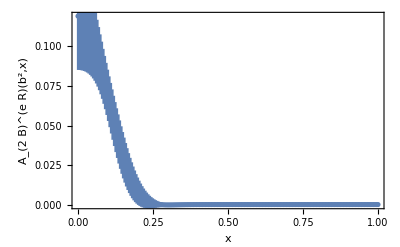

```mathematica
FourierA2bReeta[9,-4,6,3,8]
```

```mathematica
dataforfitA2B = Select[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->-2, bNum->even}],{etav, Pb32by2Pi, bsquare,data}],#[[1]]>=3&&#[[1]]<=7&&#[[3]]>=8&];
```

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,e_,f_}]:=(a^x1)*Exp[-c*x2^2]*Exp[-(d^x1)*e*(x3^f)];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, Pb32by2Pi, bsquare,{a,c, d,e,f}],{{a, 0.73703086},{c,0.000282}, {d,1.1452}, {e,0.148}, {f,0.629}},{n,Pb32by2Pi, bsquare}, modelfitA2B]
```

{FitParameters→{⟨0.7963(66)⟩_(RowBox[{),⟨160(280) × 10⟩_(RowBox[{),⟨1.1575(39)⟩_(RowBox[{),⟨0.2084(92)⟩_(RowBox[{),⟨0.558(12)⟩_(RowBox[{)},chisquareDoF→3.20855}

```mathematica
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->-1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=6&&Sqrt[#[[2]]^2+#[[3]]^2]>=3&];
```

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*x1*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, -8.15},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨1.179(66)⟩_(RowBox[{),⟨0.00865(29)⟩_(RowBox[{),⟨0.0577(16)⟩_(RowBox[{),⟨0.4560(83)⟩_(RowBox[{)},chisquareDoF→4.77692}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*(x1*x2)^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨0.690(37)⟩_(RowBox[{),⟨0.001218(41)⟩_(RowBox[{),⟨0.0567(15)⟩_(RowBox[{),⟨0.3831(81)⟩_(RowBox[{)},chisquareDoF→7.03247}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*Sqrt[x1]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨1.556(90)⟩_(RowBox[{),⟨0.02262(76)⟩_(RowBox[{),⟨0.0579(16)⟩_(RowBox[{),⟨0.4960(84)⟩_(RowBox[{)},chisquareDoF→4.6812}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨1.43(11)⟩_(RowBox[{),⟨0.0165(35)⟩_(RowBox[{),⟨0.0579(16)⟩_(RowBox[{),⟨0.484(12)⟩_(RowBox[{),⟨0.65(12)⟩_(RowBox[{)},chisquareDoF→4.58919}

```mathematica
Print["P1=-3"]


modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}},{n,bL,bT}, modelfitA2B]
```

P1=-3

{FitParameters→{⟨1.43(11)⟩_(RowBox[{),⟨0.0165(35)⟩_(RowBox[{),⟨0.0579(16)⟩_(RowBox[{),⟨0.484(12)⟩_(RowBox[{),⟨0.65(12)⟩_(RowBox[{)},chisquareDoF→4.58919}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_, h_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*h^(-f*x1);
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g, h}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}, {h,0.001}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨1.68(27)⟩_(RowBox[{),⟨0.0223(89)⟩_(RowBox[{),⟨0.0753(45)⟩_(RowBox[{),⟨-0.374(31)⟩_(RowBox[{),⟨0.62(21)⟩_(RowBox[{),⟨0.0549(60)⟩_(RowBox[{)},chisquareDoF→1.47921}

```mathematica
Print["P1=-3"]
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_, h_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*h^(-f*x1);
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g, h}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}, {h,0.001}},{n,bL,bT}, modelfitA2B]
```

P1=-3

{FitParameters→{⟨1.68(27)⟩_(RowBox[{),⟨0.0223(89)⟩_(RowBox[{),⟨0.0753(45)⟩_(RowBox[{),⟨-0.374(31)⟩_(RowBox[{),⟨0.62(21)⟩_(RowBox[{),⟨0.0549(60)⟩_(RowBox[{)},chisquareDoF→1.47921}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_, h_, j_}]:=a*Exp[-c*(x1^g+j)*x2^2]*Exp[-d*x3^2]*h^(-f*x1);
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g, h, k}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}, {h,0.001}, {k,0.001}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨1.62(23)⟩_(RowBox[{),⟨0.067(24)⟩_(RowBox[{),⟨0.0736(54)⟩_(RowBox[{),⟨2.91(21)⟩_(RowBox[{),⟨-0.9 ± 3.2⟩_(RowBox[{),⟨-0.806(44)⟩_(RowBox[{),⟨0.70(79)⟩_(RowBox[{)},chisquareDoF→75.7968}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_}]:=a*Exp[-c*(x1+g)*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨1.68(27)⟩_(RowBox[{),⟨0.0068(26)⟩_(RowBox[{),⟨0.0753(45)⟩_(RowBox[{),⟨0.512(23)⟩_(RowBox[{),⟨3.2(39)⟩_(RowBox[{)},chisquareDoF→1.47174}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*(Exp[-c*x2^2]*Exp[-d*x3^2])^(x1);
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d}],{{a, -8.15},{c,0.08}, {d,0.06}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨0.076(15)⟩_(RowBox[{),⟨0.0186(15)⟩_(RowBox[{),⟨0.0197(28)⟩_(RowBox[{)},chisquareDoF→2.22642}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, -8.15},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨2.50(33)⟩_(RowBox[{),⟨0.0765(44)⟩_(RowBox[{),⟨0.0753(45)⟩_(RowBox[{),⟨0.571(18)⟩_(RowBox[{)},chisquareDoF→1.6436}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-c*x1*x2^2]*Exp[-d*x3^2];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d}],{{a, -8.15},{c,0.08}, {d,0.06}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨0.0590(54)⟩_(RowBox[{),⟨0.01383(61)⟩_(RowBox[{),⟨0.1188(93)⟩_(RowBox[{)},chisquareDoF→23.8714}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*(Exp[-c*x2^2]*Exp[-d*x3^2])^x1;
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d}],{{a, -8.15},{c,0.08}, {d,0.06}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨0.0974(78)⟩_(RowBox[{),⟨0.01666(62)⟩_(RowBox[{),⟨0.0192(12)⟩_(RowBox[{)},chisquareDoF→12.2}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-Tanh[c*x1]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, -8.15},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨1.15(38)⟩_(RowBox[{),⟨0.0152(16)⟩_(RowBox[{),⟨0.088(12)⟩_(RowBox[{),⟨0.474(43)⟩_(RowBox[{)},chisquareDoF→0.84182}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*x1*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, -8.15},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨1.15(38)⟩_(RowBox[{),⟨0.0151(16)⟩_(RowBox[{),⟨0.088(12)⟩_(RowBox[{),⟨0.473(43)⟩_(RowBox[{)},chisquareDoF→0.841819}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_}]:=a*Exp[-c*x1*x2^2]*Exp[-d*x1*x3^2];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d}],{{a, -8.15},{c,0.08}, {d,0.06}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨0.0974(78)⟩_(RowBox[{),⟨0.01666(62)⟩_(RowBox[{),⟨0.0192(12)⟩_(RowBox[{)},chisquareDoF→12.2}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*x1*x2^2]*Exp[-d*x3^2]*f^(-x1);
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, -8.15},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨1.32(16)⟩_(RowBox[{),⟨0.01142(67)⟩_(RowBox[{),⟨0.0746(43)⟩_(RowBox[{),⟨1.611(27)⟩_(RowBox[{)},chisquareDoF→1.54749}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*x1*x2^2]*Exp[-d*x1*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, -8.15},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitA2B]
```

{FitParameters→{⟨-289(15)⟩_(RowBox[{),⟨4.20(11)⟩_(RowBox[{),⟨0.907(39)⟩_(RowBox[{),⟨-0.34(30)⟩_(RowBox[{)},chisquareDoF→104.565}

```mathematica
dataforfitA2Bodd = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->-2, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=6&&Sqrt[#[[2]]^2+#[[3]]^2]>=3&];
```

```mathematica
modelfitA2Bodd[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*x2*Exp[-c*x1*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2Bodd =JackknifeFit4D[dataforfitA2Bodd,modelfitA2Bodd[n, bL,bT,{a,c, d, f}],{{a, -8.15},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitA2Bodd]
```

{FitParameters→{⟨0.140(39)⟩_(RowBox[{),⟨0.00663(48)⟩_(RowBox[{),⟨0.0485(60)⟩_(RowBox[{),⟨0.513(46)⟩_(RowBox[{)},chisquareDoF→0.672471}

```mathematica
fitParasA2Bodd=FitParameters/. fitJKA2Bodd
(12*fitParasA2Bodd[[2]])-fitParasA2Bodd[[3]]
```

{⟨0.140(39)⟩_(RowBox[{),⟨0.00663(48)⟩_(RowBox[{),⟨0.0485(60)⟩_(RowBox[{),⟨0.513(46)⟩_(RowBox[{)}

⟨0.0310(81)⟩_(RowBox[{)

```mathematica
SiversShift[b2_,P1_,etaminForFit_, bminForFit_, etafit_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&#[[1]]<=10&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&#[[1]]<=10&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
(*dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&];*)
dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&#[[1]]<=10&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fits!"];
Print["",etaminForFit," are SELECTED for fit!"];
modelfitA12B[x1_,x2_, x3_,{a_,c_, d_, f_}]:=a*Exp[-f*x1]*Exp[-c*x1*x2^2]*Exp[-d*x3^2];
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-f*x1]*Exp[-c*x1*x2^2]*Exp[-d*x3^2];
modelfitImA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-f*x1]*x2*Exp[-c*x2^2]*Exp[-d*x3^2];
fitJKA12B =JackknifeFit4D[dataforfitA12B,modelfitA12B[n, bL,bT,{a,c, d,f}],{{a, -8.15},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.5},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit4D[dataforfitImA2B,modelfitImA2B[n, bL,bT,{a,c, d,f}],{{a, 0.1},{c,0.08}, {d,0.06}, {f,0.6}},{n,bL,bT}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitdA12B =fitParasA12B[[4]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitdA2B =fitParasA2B[[4]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
fitdImA2B =fitParasImA2B[[4]];
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1}],MN][[1]];
A12BReprefactorPb=((etafit*fitbA12B)-fitcA12B)/(P1^2);
reducedratioA12B=fitaA12B/(Sqrt[2*A12BReprefactorPb]);
fourierA12B[x_, {reducedr_, A12BReprefactPb_, cA12B_, dA12B_}] :=Exp[-((x^2)/(4*A12BReprefactPb))-cA12B*b2]*Exp[-dA12B*etafit]*reducedr;
A2BReprefactorPb=((etafit*fitbA2B)-fitcA2B)/(P1^2);
reducedratioA2B=fitaA2B/(Sqrt[2*A2BReprefactorPb]);
fourierA2B[x_, {reducedr_, A2BReprefactPb_, cA2B_, dA2B_}] :=Exp[-((x^2)/(4*A2BReprefactPb))-cA2B*b2]*Exp[-dA2B*etafit]*reducedr;

A2BImprefactorPb=((fitbImA2B)-fitcImA2B)/(P1^2);
reducedratioImA2B=fitaImA2B/(2*Sqrt[2]*A2BImprefactorPb^(3/2));
fourierImA2B[x_, {reducedr_,  A2BImReprefactPb_, cIMA2B_, dImA2B_}] :=x*Exp[-((x^2)/(4*A2BImReprefactPb))-cIMA2B*b2]*Exp[-dImA2B*etafit]*reducedr;

massterm=-MassN*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
fourierA12Bforx = modelfitJackkifex[fourierA12B,{reducedratioA12B, A12BReprefactorPb, fitcA12B, fitdA12B}, x];
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{reducedratioA2B, A2BReprefactorPb, fitcA2B, fitdA2B}, x];
fourierIMA2Bforx=modelfitJackkifex[fourierImA2B,{reducedratioImA2B, A2BImprefactorPb, fitcImA2B, fitdImA2B}, x];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
Print["",etafit," is SELECTED for plot!"];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
(*modelforxintgralA12B[b_]:=ArcTan[Sinh[π/(2 b)]];
xintegralA12B=modelJackk[modelforxintgralA12B, fitbA12B, fitaA12B* Sqrt[2/π]/(b2II+fitcA12B)];
Print[" ",OutputForm[xintegralA12B]];
Print["", OutputForm[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]]]];*)
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
(*modelforxintgralA2B[b_]:=ArcTan[Sinh[π/(2 b)]];
modelforxintgralA2BIM[b_]:=(2-2*Exp[-1/(4b)]);
xintegralA2B=modelJackk[modelforxintgralA2B, fitbA2B, fitaA2B* Sqrt[2/π]/(b2II+fitcA2B)]-modelJackk[modelforxintgralA2BIM, fitbImA2B, fitaImA2B/(22*Sqrt[2]*Sqrt[fitbImA2B]*(b2II+fitcImA2B))];
Print[" ",OutputForm[xintegralA2B]];
Print["", OutputForm[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]]]];*)
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,0.1}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift]
(*Print[" ",OutputForm[massterm*xintegralA12B/xintegralA2B]];
Print["", OutputForm[(massterm*MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A12B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]])/(MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->A2B,PL->P1,etav->etavalue, bNum->even, bsquare->b2, Pb32by2Pi->0}],data][[1]])]];*)
(*Export["/Users/hariprashadravikumar/Downloads/Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

3 are SELECTED for fits!

3 are SELECTED for fit!

Fitting:    -> () = {⟨-0.184(20)⟩_(2902J), ⟨0.0129(12)⟩_(2902J), ⟨0.0505(27)⟩_(2902J), ⟨0.432(23)⟩_(2902J)}, chisquareDoF = 1.19841
 Fitting:    -> () = {⟨0.819(21)⟩_(2902J), ⟨0.01207(29)⟩_(2902J), ⟨0.04706(89)⟩_(2902J), ⟨0.4421(58)⟩_(2902J)}, chisquareDoF = 7.79729
 Fitting:   -> () = {⟨0.0631(35)⟩_(2902J), ⟨0.00908(26)⟩_(2902J), ⟨0.0391(20)⟩_(2902J), ⟨0.360(13)⟩_(2902J)} chisquareDoF = 2.27908
  = 9  = -2

6 is SELECTED for plot!

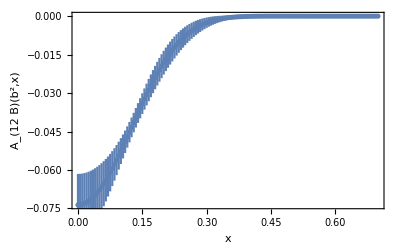

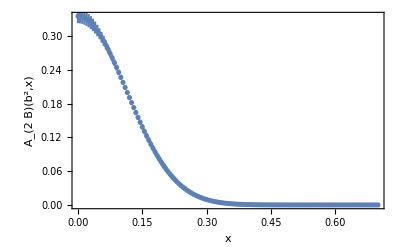

Sivers shift in GeV

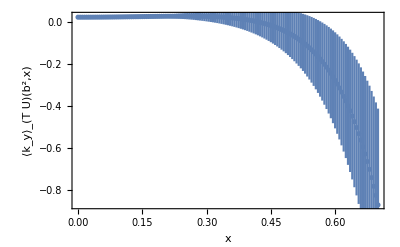

```mathematica
SiversShift[9,-2,3, 3, 6]
```

3 are SELECTED for fits!

3 are SELECTED for fit!

Fitting:    -> () = {⟨-0.207(20)⟩_(2902J), ⟨0.0121(11)⟩_(2902J), ⟨0.0490(25)⟩_(2902J), ⟨0.401(21)⟩_(2902J)}, chisquareDoF = 0.996772
 Fitting:    -> () = {⟨0.7771(99)⟩_(2902J), ⟨0.00968(13)⟩_(2902J), ⟨0.04064(44)⟩_(2902J), ⟨0.4117(30)⟩_(2902J)}, chisquareDoF = 22.4665
 Fitting:   -> () = {⟨0.0327(19)⟩_(2902J), ⟨0.00827(26)⟩_(2902J), ⟨0.0363(20)⟩_(2902J), ⟨0.331(13)⟩_(2902J)} chisquareDoF = 1.64432
  = 9  = -1

12 is SELECTED for plot!

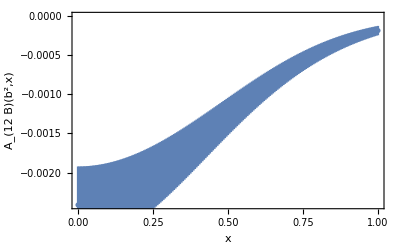

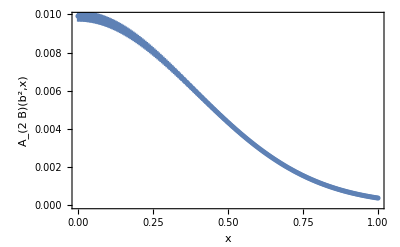

Sivers shift in GeV

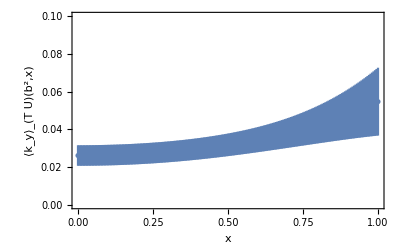

```mathematica
SiversShift[9,-1,3, 3, 12]
```

3 are SELECTED for fits!

3 are SELECTED for fit!

Fitting:    -> () = {⟨-0.184(20)⟩_(2902J), ⟨0.0129(12)⟩_(2902J), ⟨0.0505(27)⟩_(2902J), ⟨0.432(23)⟩_(2902J)}, chisquareDoF = 1.19841
 Fitting:    -> () = {⟨0.819(21)⟩_(2902J), ⟨0.01207(29)⟩_(2902J), ⟨0.04706(89)⟩_(2902J), ⟨0.4421(58)⟩_(2902J)}, chisquareDoF = 7.79729
 Fitting:   -> () = {⟨0.0631(35)⟩_(2902J), ⟨0.00908(26)⟩_(2902J), ⟨0.0391(20)⟩_(2902J), ⟨0.360(13)⟩_(2902J)} chisquareDoF = 2.27908
  = 9  = -2

12 is SELECTED for plot!

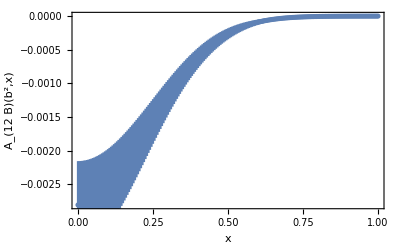

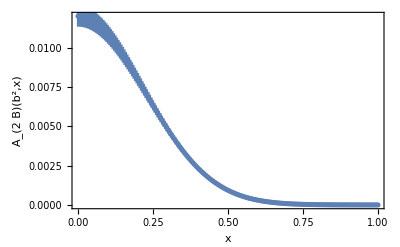

Sivers shift in GeV

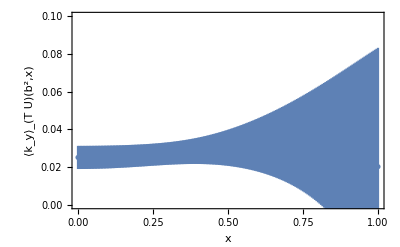

```mathematica
SiversShift[9,-2,3, 3, 12]
```

3 are SELECTED for fits!

3 are SELECTED for fit!

Fitting:    -> () = {⟨-0.153(37)⟩_(2902J), ⟨0.0166(29)⟩_(2902J), ⟨0.0515(58)⟩_(2902J), ⟨0.479(58)⟩_(2902J)}, chisquareDoF = 0.608367
 Fitting:    -> () = {⟨0.843(55)⟩_(2902J), ⟨0.01627(85)⟩_(2902J), ⟨0.0552(27)⟩_(2902J), ⟨0.467(15)⟩_(2902J)}, chisquareDoF = 2.56179
 Fitting:   -> () = {⟨0.0954(85)⟩_(2902J), ⟨0.01060(49)⟩_(2902J), ⟨0.0402(32)⟩_(2902J), ⟨0.411(24)⟩_(2902J)} chisquareDoF = 0.912037
  = 9  = -3

12 is SELECTED for plot!

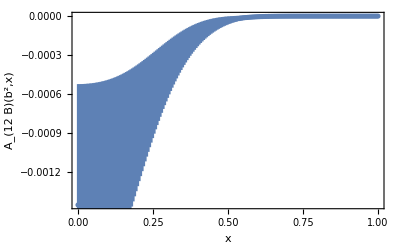

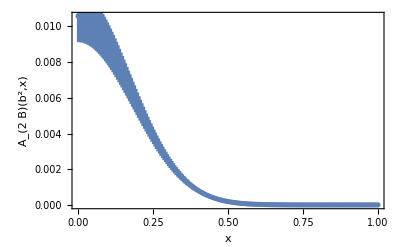

Sivers shift in GeV

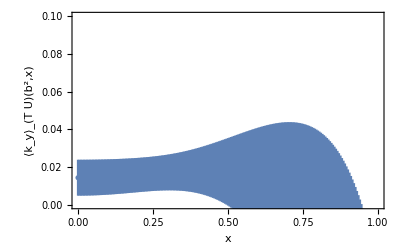

```mathematica
SiversShift[9,-3,3, 3, 12]
```

3 are SELECTED for fits!

3 are SELECTED for fit!

Fitting:    -> () = {⟨-0.15(36)⟩_(2902J), ⟨0.028(13)⟩_(2902J), ⟨0.058(26)⟩_(2902J), ⟨0.80(32)⟩_(2902J)}, chisquareDoF = 0.486992
 Fitting:    -> () = {⟨0.80(14)⟩_(2902J), ⟨0.0221(27)⟩_(2902J), ⟨0.0652(75)⟩_(2902J), ⟨0.441(37)⟩_(2902J)}, chisquareDoF = 0.973692
 Fitting:   -> () = {⟨0.107(23)⟩_(2902J), ⟨0.0140(14)⟩_(2902J), ⟨0.0448(79)⟩_(2902J), ⟨0.402(57)⟩_(2902J)} chisquareDoF = 0.448001
  = 9  = -4

12 is SELECTED for plot!

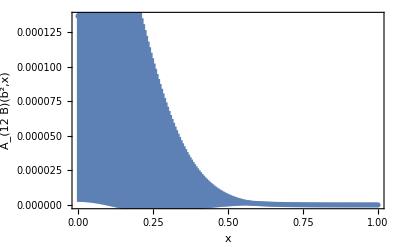

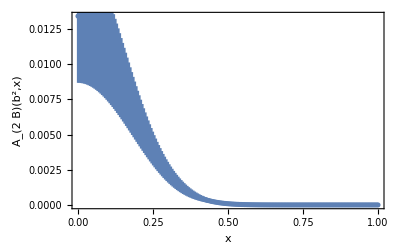

Sivers shift in GeV

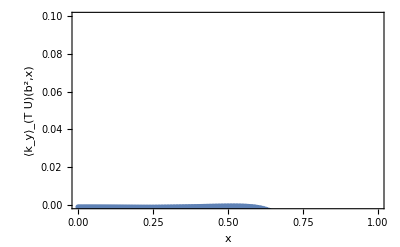

```mathematica
SiversShift[9,-4,3, 3, 12]
```

3 are SELECTED for fits!

3 are SELECTED for fit!

Fitting:    -> () = {⟨-0.184(20)⟩_(2902J), ⟨0.0129(12)⟩_(2902J), ⟨0.0505(27)⟩_(2902J), ⟨0.432(23)⟩_(2902J)}, chisquareDoF = 1.19841
 Fitting:    -> () = {⟨0.819(21)⟩_(2902J), ⟨0.01207(29)⟩_(2902J), ⟨0.04706(89)⟩_(2902J), ⟨0.4421(58)⟩_(2902J)}, chisquareDoF = 7.79729
 Fitting:   -> () = {⟨0.0631(35)⟩_(2902J), ⟨0.00908(26)⟩_(2902J), ⟨0.0391(20)⟩_(2902J), ⟨0.360(13)⟩_(2902J)} chisquareDoF = 2.27908
  = 9  = -2

15 is SELECTED for plot!

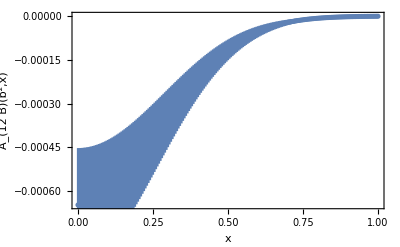

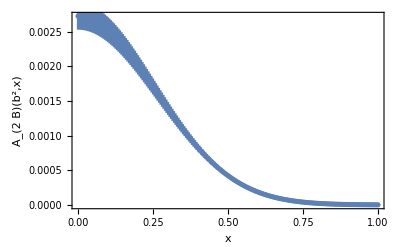

Sivers shift in GeV

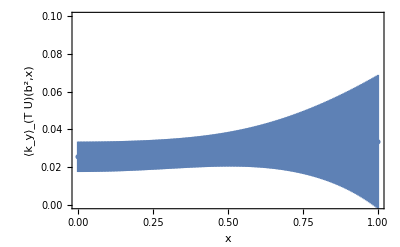

```mathematica
SiversShift[9,-2,3, 3, 15]
```

3 are SELECTED for Re A2B!

3 are SELECTED for fit!

Fitting:    -> () = {⟨-0.224(17)⟩_(2902J), ⟨0.0167(13)⟩_(2902J), ⟨0.0720(41)⟩_(2902J), ⟨0.349(15)⟩_(2902J)}, chisquareDoF = 3.90985
 Fitting:    -> () = {⟨0.794(19)⟩_(2902J), ⟨0.01218(28)⟩_(2902J), ⟨0.04675(87)⟩_(2902J), ⟨0.4331(54)⟩_(2902J)}, chisquareDoF = 9.08784
 Fitting:   -> () = {⟨0.0690(32)⟩_(2902J), ⟨0.01200(38)⟩_(2902J), ⟨0.0511(23)⟩_(2902J), ⟨0.2867(97)⟩_(2902J)} chisquareDoF = 7.63147
  = 9  = -2

9 is SELECTED for plot!

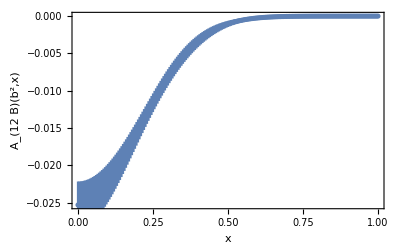

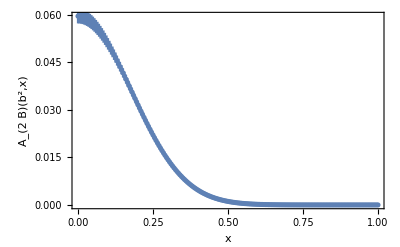

Sivers shift in GeV

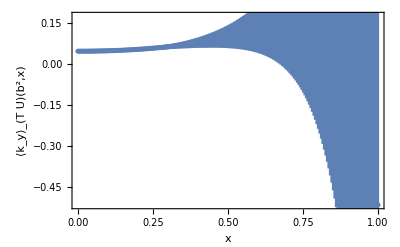

```mathematica
SiversShift[9,-2,3, 3, 9]
```

3 are SELECTED for Re A2B!

3 are SELECTED for fit!

Fitting:    -> () = {⟨-0.188(32)⟩_(2902J), ⟨0.0206(30)⟩_(2902J), ⟨0.077(11)⟩_(2902J), ⟨0.381(36)⟩_(2902J)}, chisquareDoF = 1.21734
 Fitting:    -> () = {⟨0.827(51)⟩_(2902J), ⟨0.01637(82)⟩_(2902J), ⟨0.0550(27)⟩_(2902J), ⟨0.462(15)⟩_(2902J)}, chisquareDoF = 3.1651
 Fitting:   -> () = {⟨0.1101(74)⟩_(2902J), ⟨0.01452(67)⟩_(2902J), ⟨0.0549(40)⟩_(2902J), ⟨0.334(17)⟩_(2902J)} chisquareDoF = 3.56397
  = 9  = -3

9 is SELECTED for plot!

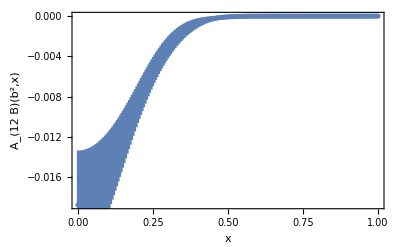

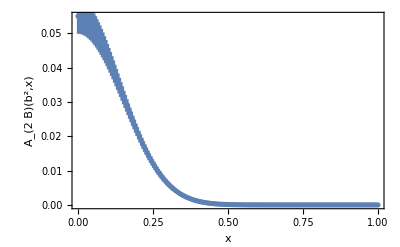

Sivers shift in GeV

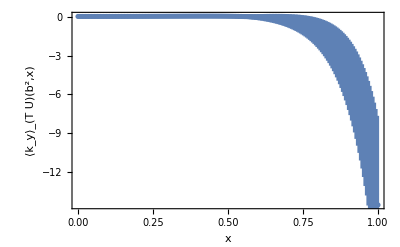

```mathematica
SiversShift[9,-3,3, 3, 9]
```

```mathematica
SiversShift[9,-1,3, 3, 9]
```

3 are SELECTED for Re A2B!

3 are SELECTED for fit!

$Aborted

3 are SELECTED for Re A2B!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.368(61)⟩_(2902J), ⟨0.0209(27)⟩_(2902J), ⟨0.165(24)⟩_(2902J), ⟨0.304(22)⟩_(2902J)}, chisquareDoF = 2.6912
 Fitting:    -> () = {⟨1.32(16)⟩_(2902J), ⟨0.01142(67)⟩_(2902J), ⟨0.0746(43)⟩_(2902J), ⟨0.477(17)⟩_(2902J)}, chisquareDoF = 1.54749
 Fitting:   -> () = {⟨0.116(13)⟩_(2902J), ⟨0.01665(93)⟩_(2902J), ⟨0.120(15)⟩_(2902J), ⟨0.287(17)⟩_(2902J)} chisquareDoF = 4.79516
  = 9  = -2

9 is SELECTED for plot!

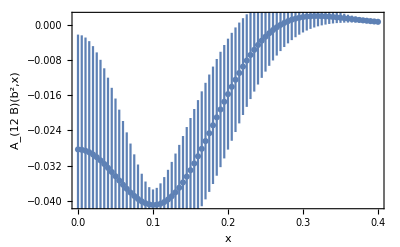

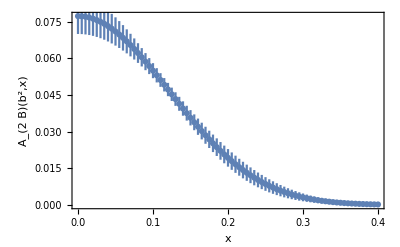

Sivers shift in GeV

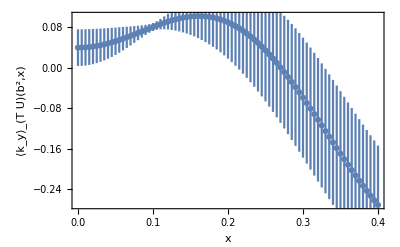

```mathematica
SiversShift[9,-2,6, 3, 9]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.27(13)⟩_(2902J), ⟨0.0125(26)⟩_(2902J), ⟨0.0637(91)⟩_(2902J), ⟨0.476(64)⟩_(2902J)}, chisquareDoF = 0.987155
 Fitting:    -> () = {⟨1.32(16)⟩_(2902J), ⟨0.01142(67)⟩_(2902J), ⟨0.0746(43)⟩_(2902J), ⟨0.477(17)⟩_(2902J)}, chisquareDoF = 1.54749
 Fitting:   -> () = {⟨0.140(39)⟩_(2902J), ⟨0.00663(48)⟩_(2902J), ⟨0.0485(60)⟩_(2902J), ⟨0.513(46)⟩_(2902J)} chisquareDoF = 0.672471
  = 9  = -2

12 is SELECTED for plot!

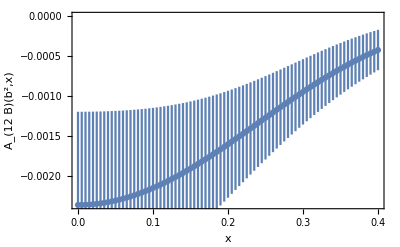

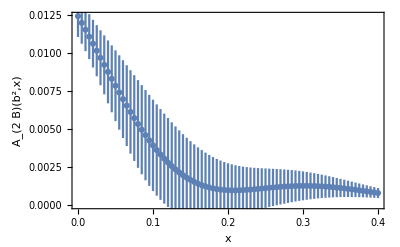

Sivers shift in GeV

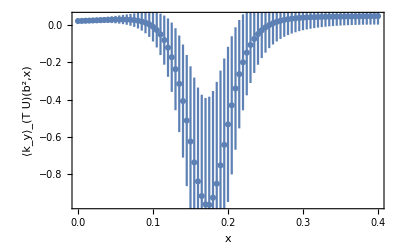

```mathematica
SiversShift[9,-2,6, 3, 12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.27(13)⟩_(2902J), ⟨0.0125(26)⟩_(2902J), ⟨0.0637(91)⟩_(2902J), ⟨0.476(64)⟩_(2902J)}, chisquareDoF = 0.987155
 Fitting:    -> () = {⟨1.32(16)⟩_(2902J), ⟨0.01142(67)⟩_(2902J), ⟨0.0746(43)⟩_(2902J), ⟨0.477(17)⟩_(2902J)}, chisquareDoF = 1.54749
 Fitting:   -> () = {⟨0.140(39)⟩_(2902J), ⟨0.00663(48)⟩_(2902J), ⟨0.0485(60)⟩_(2902J), ⟨0.513(46)⟩_(2902J)} chisquareDoF = 0.672471
  = 9  = -2

12 is SELECTED for plot!

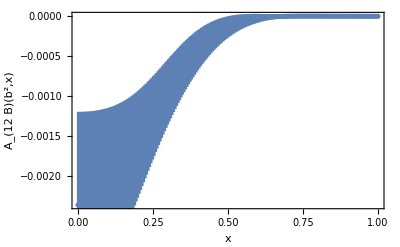

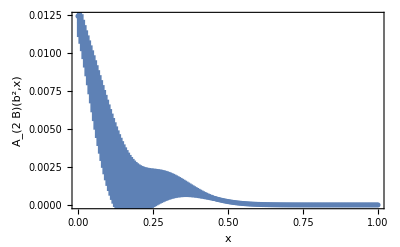

Sivers shift in GeV

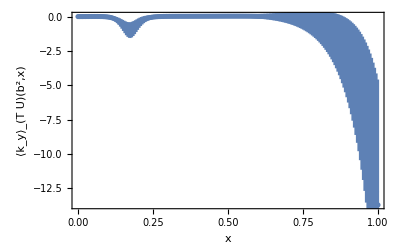

```mathematica
SiversShift[9,-2,6, 3, 12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.27(13)⟩_(2902J), ⟨0.0125(26)⟩_(2902J), ⟨0.0637(91)⟩_(2902J), ⟨0.476(64)⟩_(2902J)}, chisquareDoF = 0.987155
 Fitting:    -> () = {⟨1.32(16)⟩_(2902J), ⟨0.01142(67)⟩_(2902J), ⟨0.0746(43)⟩_(2902J), ⟨0.477(17)⟩_(2902J)}, chisquareDoF = 1.54749
 Fitting:   -> () = {⟨0.140(39)⟩_(2902J), ⟨0.00663(48)⟩_(2902J), ⟨0.0485(60)⟩_(2902J), ⟨0.513(46)⟩_(2902J)} chisquareDoF = 0.672471
  = 9  = -2

15 is SELECTED for plot!

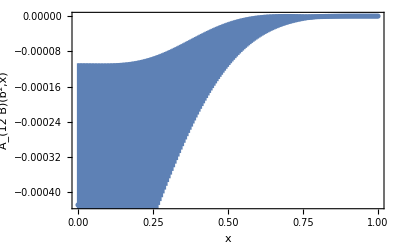

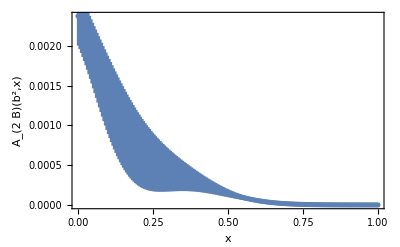

Sivers shift in GeV

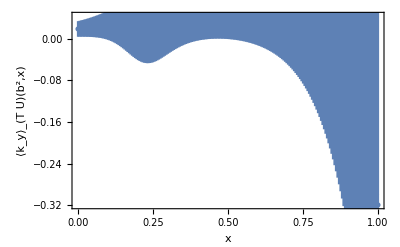

```mathematica
SiversShift[9,-2,6, 3, 15]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.12(30)⟩_(2902J), ⟨0.0143(58)⟩_(2902J), ⟨0.058(18)⟩_(2902J), ⟨0.55(18)⟩_(2902J)}, chisquareDoF = 0.619994
 Fitting:    -> () = {⟨1.15(38)⟩_(2902J), ⟨0.0151(16)⟩_(2902J), ⟨0.088(12)⟩_(2902J), ⟨0.473(43)⟩_(2902J)}, chisquareDoF = 0.841819
 Fitting:   -> () = {⟨0.109(74)⟩_(2902J), ⟨0.00647(96)⟩_(2902J), ⟨0.053(15)⟩_(2902J), ⟨0.506(92)⟩_(2902J)} chisquareDoF = 0.433119
  = 9  = -3

12 is SELECTED for plot!

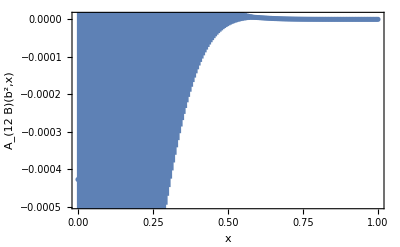

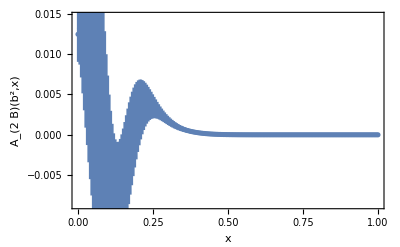

Sivers shift in GeV

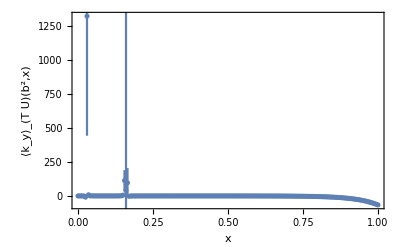

```mathematica
SiversShift[9,-3,6, 3, 12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () =                  3
{⟨-2.731(56) × 10 ⟩_(2902J), ⟨-0.932(63)⟩_(2902J), ⟨9.07(13)⟩_(2902J), ⟨-17.74(70)⟩_(2902J)}, chisquareDoF = 10.3248
 Fitting:    -> () = {⟨0.89(70)⟩_(2902J), ⟨0.0162(29)⟩_(2902J), ⟨0.069(19)⟩_(2902J), ⟨0.496(93)⟩_(2902J)}, chisquareDoF = 0.504828
 Fitting:   -> () = {⟨0.05 ± 0.11⟩_(2902J), ⟨0.0120(57)⟩_(2902J), ⟨0.078(79)⟩_(2902J), ⟨0.37(18)⟩_(2902J)} chisquareDoF = 0.458725
  = 9  = -4

12 is SELECTED for plot!

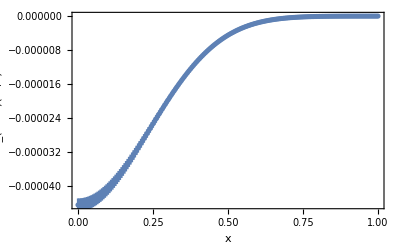

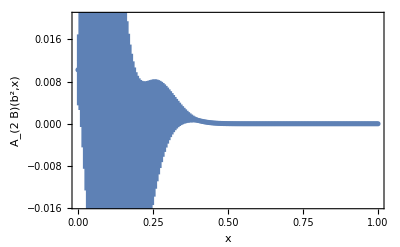

Sivers shift in GeV

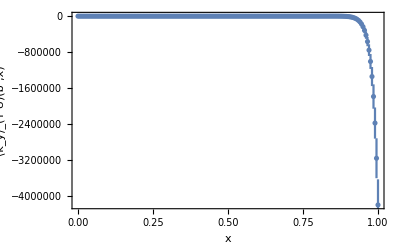

```mathematica
SiversShift[9,-4,6, 3, 12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.27(13)⟩_(2902J), ⟨0.0125(26)⟩_(2902J), ⟨0.0637(91)⟩_(2902J), ⟨0.476(64)⟩_(2902J)}, chisquareDoF = 0.987155
 Fitting:    -> () = {⟨1.32(16)⟩_(2902J), ⟨0.01142(67)⟩_(2902J), ⟨0.0746(43)⟩_(2902J), ⟨0.477(17)⟩_(2902J)}, chisquareDoF = 1.54749
 Fitting:   -> () = {⟨0.140(39)⟩_(2902J), ⟨0.00663(48)⟩_(2902J), ⟨0.0485(60)⟩_(2902J), ⟨0.513(46)⟩_(2902J)} chisquareDoF = 0.672471
  = 9  = -2

8 is SELECTED for plot!

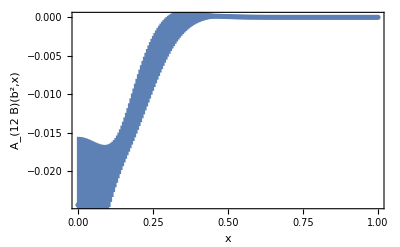

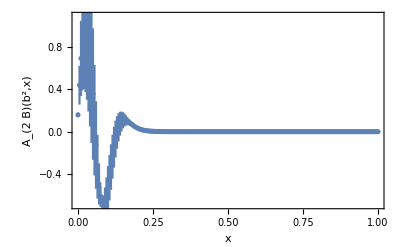

Sivers shift in GeV

-Graphics-

```mathematica
SiversShift[9,-2,6, 3, 8]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.12(30)⟩_(2902J), ⟨0.0143(58)⟩_(2902J), ⟨0.058(18)⟩_(2902J), ⟨0.55(18)⟩_(2902J)}, chisquareDoF = 0.619994
 Fitting:    -> () = {⟨1.15(38)⟩_(2902J), ⟨0.0151(16)⟩_(2902J), ⟨0.088(12)⟩_(2902J), ⟨0.473(43)⟩_(2902J)}, chisquareDoF = 0.841819
 Fitting:   -> () = {⟨0.109(74)⟩_(2902J), ⟨0.00647(96)⟩_(2902J), ⟨0.053(15)⟩_(2902J), ⟨0.506(92)⟩_(2902J)} chisquareDoF = 0.433119
  = 9  = -3

8 is SELECTED for plot!

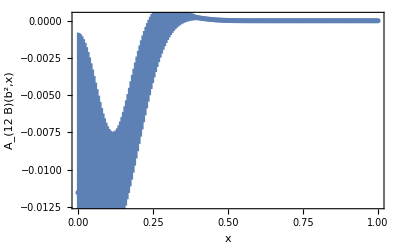

-Graphics-

Sivers shift in GeV

-Graphics-

```mathematica
SiversShift[9,-3,6, 3, 8]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () =                  3
{⟨-2.731(56) × 10 ⟩_(2902J), ⟨-0.932(63)⟩_(2902J), ⟨9.07(13)⟩_(2902J), ⟨-17.74(70)⟩_(2902J)}, chisquareDoF = 10.3248
 Fitting:    -> () = {⟨0.89(70)⟩_(2902J), ⟨0.0162(29)⟩_(2902J), ⟨0.069(19)⟩_(2902J), ⟨0.496(93)⟩_(2902J)}, chisquareDoF = 0.504828
 Fitting:   -> () = {⟨0.05 ± 0.11⟩_(2902J), ⟨0.0120(57)⟩_(2902J), ⟨0.078(79)⟩_(2902J), ⟨0.37(18)⟩_(2902J)} chisquareDoF = 0.458725
  = 9  = -4

8 is SELECTED for plot!

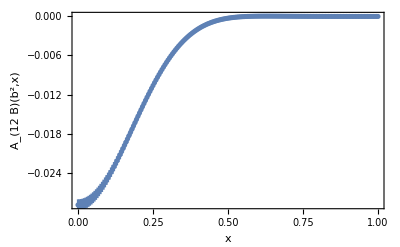

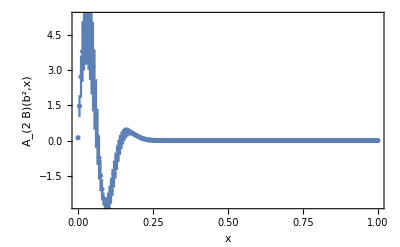

Sivers shift in GeV

-Graphics-

```mathematica
SiversShift[9,-4,6, 3, 8]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.27(13)⟩_(2902J), ⟨0.0125(26)⟩_(2902J), ⟨0.0637(91)⟩_(2902J), ⟨0.476(64)⟩_(2902J)}, chisquareDoF = 0.987155
 Fitting:    -> () = {⟨1.32(16)⟩_(2902J), ⟨0.01142(67)⟩_(2902J), ⟨0.0746(43)⟩_(2902J), ⟨0.477(17)⟩_(2902J)}, chisquareDoF = 1.54749
 Fitting:   -> () = {⟨0.140(39)⟩_(2902J), ⟨0.00663(48)⟩_(2902J), ⟨0.0485(60)⟩_(2902J), ⟨0.513(46)⟩_(2902J)} chisquareDoF = 0.672471
  = 9  = -2

10 is SELECTED for plot!

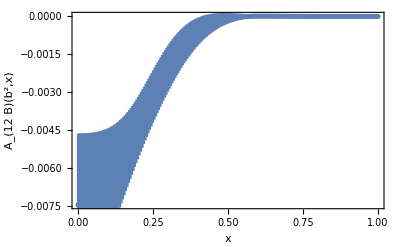

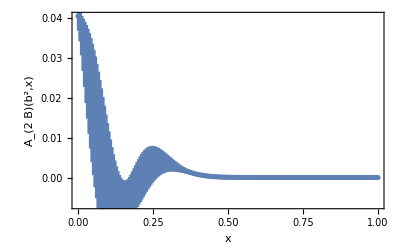

Sivers shift in GeV

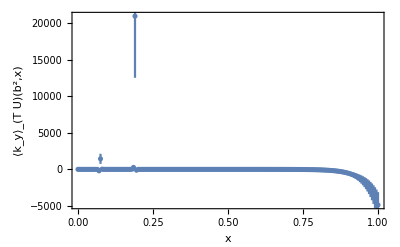

```mathematica
SiversShift[9,-2,6, 3, 10]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () = {⟨-0.12(30)⟩_(2902J), ⟨0.0143(58)⟩_(2902J), ⟨0.058(18)⟩_(2902J), ⟨0.55(18)⟩_(2902J)}, chisquareDoF = 0.619994
 Fitting:    -> () = {⟨1.15(38)⟩_(2902J), ⟨0.0151(16)⟩_(2902J), ⟨0.088(12)⟩_(2902J), ⟨0.473(43)⟩_(2902J)}, chisquareDoF = 0.841819
 Fitting:   -> () = {⟨0.109(74)⟩_(2902J), ⟨0.00647(96)⟩_(2902J), ⟨0.053(15)⟩_(2902J), ⟨0.506(92)⟩_(2902J)} chisquareDoF = 0.433119
  = 9  = -3

10 is SELECTED for plot!

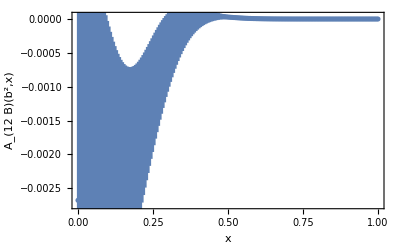

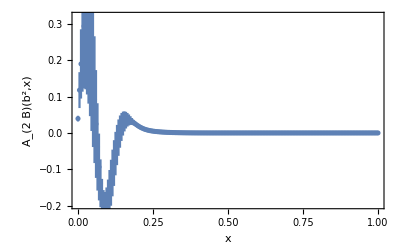

Sivers shift in GeV

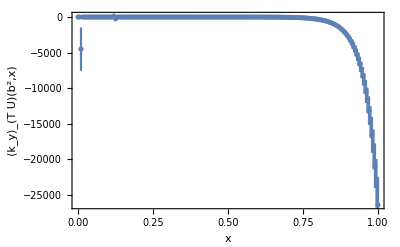

```mathematica
SiversShift[9,-3,6, 3, 10]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

Fitting:    -> () =                  3
{⟨-2.731(56) × 10 ⟩_(2902J), ⟨-0.932(63)⟩_(2902J), ⟨9.07(13)⟩_(2902J), ⟨-17.74(70)⟩_(2902J)}, chisquareDoF = 10.3248
 Fitting:    -> () = {⟨0.89(70)⟩_(2902J), ⟨0.0162(29)⟩_(2902J), ⟨0.069(19)⟩_(2902J), ⟨0.496(93)⟩_(2902J)}, chisquareDoF = 0.504828
 Fitting:   -> () = {⟨0.05 ± 0.11⟩_(2902J), ⟨0.0120(57)⟩_(2902J), ⟨0.078(79)⟩_(2902J), ⟨0.37(18)⟩_(2902J)} chisquareDoF = 0.458725
  = 9  = -4

10 is SELECTED for plot!

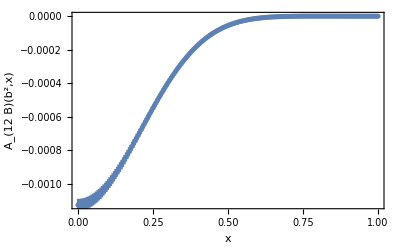

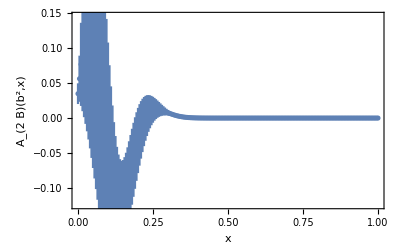

Sivers shift in GeV

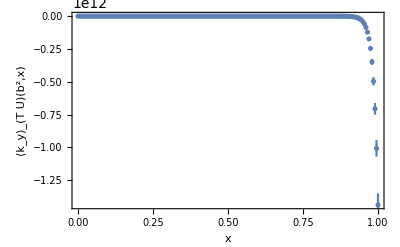

```mathematica
SiversShift[9,-4,6, 3, 10]
```